# Interesting Scribbles

Modelled on dual pendulums with a rigid stick coming from each, joined by a hinge with a pen on that hinge. This should be what it draws. Makes some nice doodles. Funny surfaces can be made by including friction. Shapes mainly vary by varying speeds of sin functions. Set tmax to something silly to make a mess!

```mathematica
(* Assumed the positions of the pendulums stay fixed, so the x of one and the y of the other could be set to 0 *)
fx[x2_,y1_]:=(x2^4+x2^2 y1^2+y1 √(-x2^2 (x2^4+y1^2 (-16+y1^2)+2 x2^2 (-8+y1^2))))/(2 x2 (x2^2+y1^2))

fy[x2_,y1_]:=(x2^2 y1+y1^3+√(-x2^2 (x2^4+y1^2 (-16+y1^2)+2 x2^2 (-8+y1^2))))/(2 (x2^2+y1^2))
```

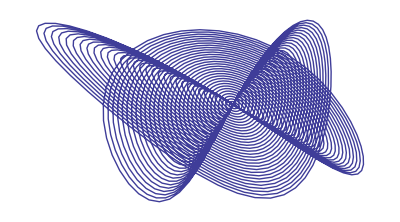

```mathematica
r:=2 (*radius*)

tmax:=400 (*run time*)

c[t_]:=(1-t/tmax)(*friction function*)

x[t_]:=1+c[t] (0.1 Sin[t] +0.1Sin[1.5t])(*x(0) + swinging function*)

y[t_]:=1+c[t] 0.2 Sin[t] (*y(0) + swinging function*)

ParametricPlot[{fx[x[t],y[t]],fy[x[t],y[t]]},{t,0.1,tmax}, Axes->None]
```